#### Main Definition

```mathematica
Reduce[!(n1<=1)]
```

n1>1

```mathematica
GridGraph[{1,1}]
```

-Graphics-

```mathematica
ClearAll[FindRandomMazeSolution]
```

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree,randomSeed,treeDepth,treeLeaves,treeLeafCount,treeSize},g=GridGraph[{m1,n1}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];tree=GraphTree[maze];treeDepth=TreeDepth[tree];
treeLeaves=TreeLeaves[tree];
treeLeafCount=TreeLeafCount[tree];
treeSize=TreeSize[tree];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"random-seed"->randomSeed,"tree"->tree,"tree-depth"->treeDepth,"tree-leaves"->treeLeaves,"tree-leaf-count"->treeLeafCount,"tree-size"->treeSize|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size"})]]:=Lookup[FindRandomMazeSolution[{m1,n1}],property]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[{m1,n1}],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph","tree","random-seed","tree-depth","tree-leaves","tree-leaf-count","tree-size"},property]]
```

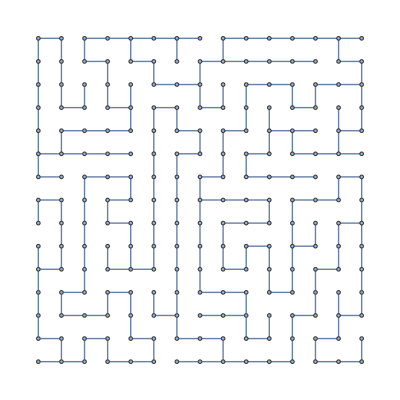
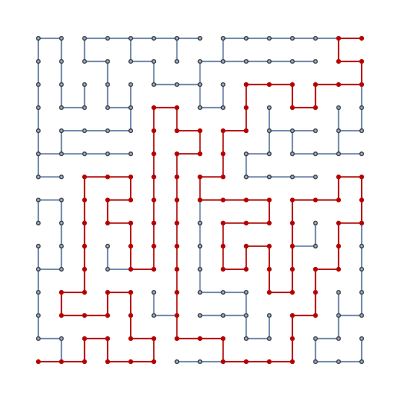
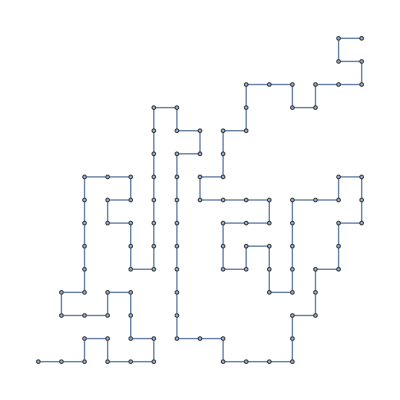
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,16,31,32,47,46,61,76,77,62,63,64,49,48,33,18,19,34,35,36,37,38,39,54,69,68,53,52,67,66,65,80,81,82,83,84,85,86,87,102,101,116,115,100,99,98,97,96,95,94,93,92,107,122,121,136,151,166,167,168,183,184,185,200,201,202,217,218,219,204,203,188,173,172,171,170,169,154,155,156,141,140,125,126,127,142,157,158,143,128,113,114,129,130,131,146,147,148,163,178,177,192,193,208,223,224,209,210,225},distance→108,start→1,end→225,shortest-path-subgraph→-Graphics-,random-seed→RandomGeneratorState[…],tree→-Graphics-,tree-depth→144,tree-leaves→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},tree-leaf-count→24,tree-size→225|>

```mathematica
FindRandomMazeSolution[{15,15}]
```

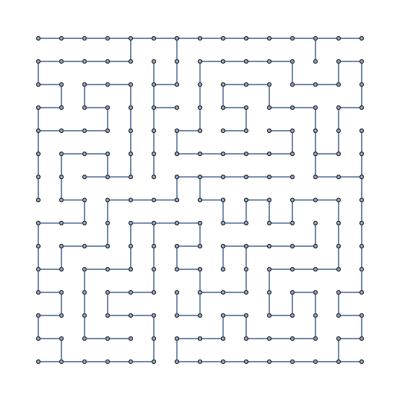

```mathematica
FindRandomMazeSolution[{15,15},"maze"]
```

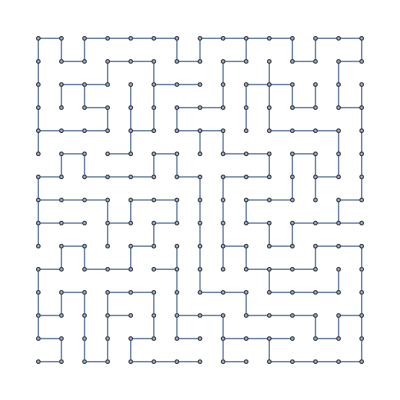
<|maze→-Graphics-,tree→-Graphics-|>

```mathematica
FindRandomMazeSolution[{15,15},{"maze","tree"}]
```

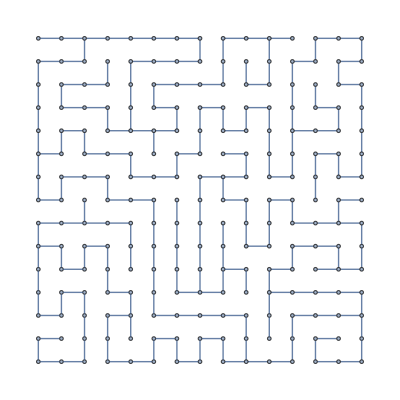
<|end→225,maze→-Graphics-,tree→-Graphics-|>

```mathematica
FindRandomMazeSolution[{15,15},{"maze","end","tree"}]
```

```mathematica
TreeLevel[-Graphics-,{-1}->"Data"]
```

{25,43,56,146,105,93,106,139,152,183,157,200,211,54,74,118,116,97,189,149,209,206,220,47,50,37,20}

```mathematica
Definition[FindRandomMazeSolution]
```

FindRandomMazeSolution[{m1_?IntegerQ,n1_?IntegerQ}]:=Block[{g,maze,m,solvedmaze},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],First[Last[Reap[Module[{stack={RandomChoice[VertexList[g]]}},Do[AnnotationValue[{g,v},Visited]=False,{v,VertexList[g]}];AnnotationValue[{g,First[stack]},Visited]=True;While[!stack=={},With[{v=First[stack]},With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;!AnnotationValue[{g,x},Visited]]},If[adj=={},stack=Rest[stack],With[{w=RandomChoice[adj]},PrependTo[stack,w];AnnotationValue[{g,w},Visited]=True;Sow[v<->w]]]]]]]]]],VertexCoordinates→GraphEmbedding[g]];maze=m;solvedmaze=HighlightGraph[m,PathGraph[FindShortestPath[m,First[VertexList[m]],Last[VertexList[m]]]]];Association[maze→maze,solved-maze→solvedmaze]]/;AllTrue[#1>0&][{m1,n1}]
 
FindRandomMazeSolution[{m1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!m1≤1,n1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!n1≤1}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],First[Last[Reap[Module[{stack={RandomChoice[VertexList[g]]}},Do[AnnotationValue[{g,v},Visited]=False,{v,VertexList[g]}];AnnotationValue[{g,First[stack]},Visited]=True;While[!stack=={},With[{v=First[stack]},With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;!AnnotationValue[{g,x},Visited]]},If[adj=={},stack=Rest[stack],With[{w=RandomChoice[adj]},PrependTo[stack,w];AnnotationValue[{g,w},Visited]=True;Sow[v<->w]]]]]]]]]],VertexCoordinates→GraphEmbedding[g]];maze=m;start=1;end=m1 n1;solvedmaze=HighlightGraph[m,PathGraph[shortestPath=FindShortestPath[m,start,end]]];tree=GraphTree[maze];shortestPathSubgraph=Subgraph[maze,shortestPath];EchoEvaluation[Association[maze→maze,solved-maze→solvedmaze,shortest-path→shortestPath,distance→GraphDistance[m,start,end],start→start,end→end,shortest-path-subgraph→shortestPathSubgraph,tree→tree]]]
 
FindRandomMazeSolution[{m1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!m1≤1,n1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!n1≤1},property_/;MatchQ[property,Alternatives@@{maze,solved-maze,shortest-path,distance,start,end,shortest-path-subgraph,tree}]]:=Lookup[FindRandomMazeSolution[{m1,n1}],property]
 
FindRandomMazeSolution[{m1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!m1≤1,n1_?(PacletSymbol[PeterBurbery/LittleChildPaclet,PeterBurbery`LittleChildPaclet`PositiveIntegerQ])/;!n1≤1},property_?VectorQ]:=AssociationMap[Function[p,Lookup[FindRandomMazeSolution[{m1,n1}],p]]][{maze,solved-maze,shortest-path,distance,start,end,shortest-path-subgraph}∩property]

RandomGeneratorState[…]

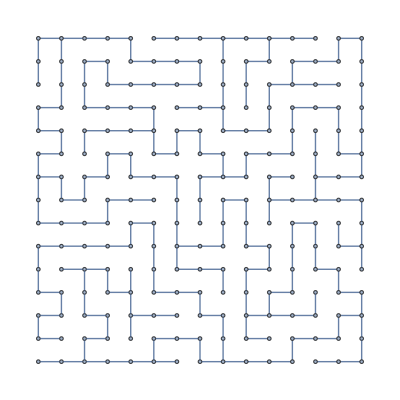
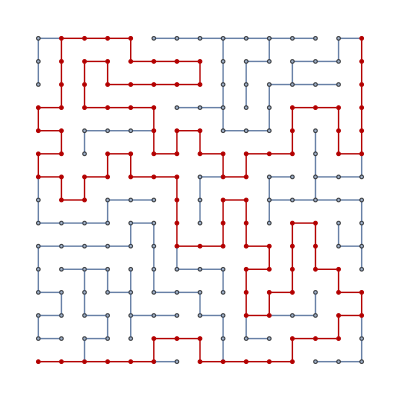
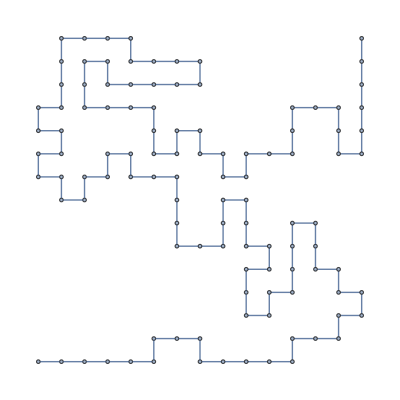
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,16,31,46,61,76,77,92,107,106,121,136,151,166,167,182,197,198,213,214,199,200,185,186,187,172,171,170,169,154,153,138,139,140,155,156,141,142,143,128,127,126,111,96,97,98,99,84,69,70,55,54,39,38,23,24,9,10,25,26,11,12,27,28,29,30,45,60,75,74,89,104,119,118,103,88,73,58,59,44,43,42,57,72,87,86,85,100,101,116,115,130,129,144,145,160,175,176,177,192,207,206,205,220,221,222,223,224,225},distance→108,start→1,end→225,shortest-path-subgraph→-Graphics-,tree→-Graphics-,tree-depth→128,random-seed→RandomGeneratorState[…]|>

```mathematica
SeedRandom[RandomGeneratorState[…]]
Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree,randomSeed,treeDepth},g=GridGraph[{15,15}];randomSeed=$RandomGeneratorState;m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=15*15(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];tree=GraphTree[maze];treeDepth=TreeDepth[tree];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"tree"->tree,"tree-depth"->treeDepth,"random-seed"->randomSeed|>]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

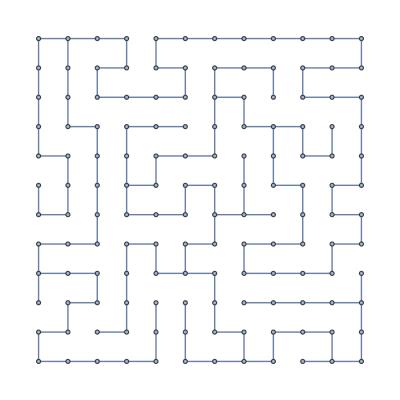
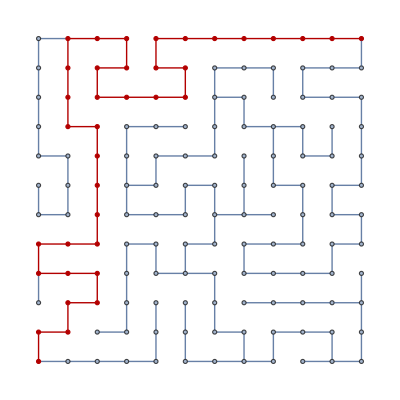
<|maze→-Graphics-,solved-maze→-Graphics-|>

```mathematica
Global`FindRandomMazeSolution[{12,12}]
```

```mathematica
{data1,data2,data3}=Table[FindRandomMazeSolution[{7,7}],3];
```

```mathematica
trees={tree1,tree2,tree3}=Table[data["tree"],{data,{data1,data2,data3}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
treeDepths=AssociationMap[TreeDepth][trees]
```

<|-Graphics-→24,-Graphics-→29,-Graphics-→27|>

```mathematica
treeSizes=AssociationMap[TreeSize][trees]
```

<|-Graphics-→49,-Graphics-→49,-Graphics-→49|>

```mathematica
treeLeafCount=AssociationMap[TreeLeafCount][trees]
```

<|-Graphics-→8,-Graphics-→8,-Graphics-→6|>

```mathematica
treeLeaves=AssociationMap[TreeLeaves][trees]
```

<|-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
data1["start"]
```

1

```mathematica
data1["end"]
```

49

```mathematica
TreeOutline[tree1]
```

```mathematica
Tree[tree1,TreeLayout->Top]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->Bottom]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->Left]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->Right]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->"BalloonEmbedding"]
```

-Graphics-

```mathematica
GraphCenter[data1["maze"]]
```

{14}

```mathematica
Tree[tree1,TreeLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->"LayeredEmbedding"]
```

-Graphics-

```mathematica
Tree[tree1,TreeLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

```mathematica
Tree[tree1,TreeElementStyle->{{}->LightRed}]
```

-Graphics-

```mathematica
UnlabeledTree[tree1]
```

-Graphics-

```mathematica
UnlabeledTree[tree1,MaxDisplayedChildren->2]
```

-Graphics-

```mathematica
UnlabeledTree[tree1,MaxDisplayedChildren->All->2]
```

-Graphics-

```mathematica
UnlabeledTree[tree1,MaxDisplayedChildren->All->1]
```

-Graphics-

```mathematica
TreeLeaves[tree1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeLeafCount[tree1]
```

8